## 1.0 initial try (abandoned)

```mathematica
spinsData=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21\\All Spins\\F21SpinsNetworkReady.xlsx"][[1]];

data=Rest[spinsData];

(* initializing the number of students, concepts, and expressions based on the data *)
nStud=Dimensions[data][[1]];
nConc=Dimensions[data][[2]];
nExp=20;

(* see note below for why we're changing this up--take too long *)

(*
(* initializing the table where the bootstrapped data will be stored *)
bootData=Table[0,nBoots,nStud];


For[i=1,i<=nBoots,i++,
For[j=1,j<=nStud,j++,
bootData[[i,j]]=data[[RandomInteger[{1,nStud}]]]
]
]

(* initializing the list of adjacency matrices we will generate--one for each bootstrapped network *)
wAdj=Table[0,nBoots,nExp,nExp];

pairsEmpty=Table[0,nExp,nExp];

pairs=pairsEmpty;

(* this is NOT working (taking way too long).  Need to split it up, so I'll probably calculate the adjacency matrices for each student individually in one loop, then make the bootstrap matrices in a separate one *)
For[m=1,m<=nBoots,m++,
Print[m];
For[i=1,i<=nStud,i++,
pairs=pairsEmpty;
For[j=1,j<=nConc,j++,
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
(* changes all single-letter entries into single-entry lists, because ContainsAny[] requires a list as an input *)
If[Length[LetterNumber[StringDelete[bootData[[m,i,j]],","]]]==0,
bootData[[m,i,j]]={bootData[[m,i,j]]}
];

(* goes through every combination of letters that appear together for a given student's set of responses, and updates the mth wAdj matrix with the number of students that used the two together *)
If[ContainsAny[LetterNumber[StringDelete[bootData[[m,i,j]],","]],{k}]&&ContainsAny[LetterNumber[StringDelete[bootData[[m,i,j]],","]],{l}]&&pairs[[k,l]]==0,
wAdj[[m,k,l]]++
]
]
]
]
]
]
*)
```

1

2

3

4

5

6

$Aborted

```mathematica
data[[1]]//MatrixForm
nStud
```

(e,f,h,j,a,n
j,h,g,k,e,t,f,i,n
n,m,l,p,o
l
b,n,f
f,j,b,n
k,j,i,h
f,j,n
n,f,j
k,h,j,i
q,r,s)

139

## 1.1 second try

### 1.1.0 Generate individual adjacency matrices

```mathematica
SetDirectory[NotebookDirectory[]];

F21spinsData=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21\\All Spins\\F21SpinsNetworkReady.xlsx"][[1]];
F22spinsData=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F22\\F22 All Spins\\F22SpinsNetworkReady.xlsx"][[1]];

data=Join[Rest[F21spinsData],Rest[F22spinsData]];

(* initializing the number of students, concepts, and expressions based on the data *)
nStud=Dimensions[data][[1]];
nConc=Dimensions[data][[2]];
nExp=20;

studAdjs=Table[0,nStud,nExp,nExp];
pairsEmpty=Table[0,nExp,nExp];
pairs=pairsEmpty;

Timing[
For[i=1,i<=nStud,i++,
pairs=pairsEmpty;
For[j=1,j<=nConc,j++,
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
If[k!=l,
(* changes all single-letter entries into single-entry lists, because ContainsAny[] requires a list as an input *)
If[Length[LetterNumber[StringDelete[data[[i,j]],","]]]==0,
data[[i,j]]={data[[i,j]]}
];

(* creates every student's individual adjacency matrix, and stores them as the ith elements of the studAdjs list of matrices *)
If[ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{k}]&&ContainsAny[LetterNumber[StringDelete[data[[i,j]],","]],{l}]&&pairs[[k,l]]==0,
studAdjs[[i,k,l]]++;
pairs[[k,l]]++
]
]
]
]
]
]
]


Export["F21+F22SpinsIndividualStudentAdjacencies.xlsx",studAdjs];
```

{445.797,Null}

### 1.1.1 Do the bootstrap process

```mathematica
Timing[

(* imports the "network ready" data *)
spinsData=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsNetworkReady.xlsx"][[1]];

(* imports the studAdjs array found in the prior section. This is so we don't have to run that code again, as it takes a while to do so *)
studAdjs=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsIndividualStudentAdjacencies.xlsx"];


data=Rest[spinsData];

(* initializing the number of students, concepts, and expressions based on the data *)
nStud=Dimensions[data][[1]];
nConc=Dimensions[data][[2]];
nExp=20;

(* initializing the number of bootstrapped networks we'll generate *)
nBoots=1000;

bootAdjs=Table[0,nBoots,nExp,nExp];

(* Here we add up a random assortment of students' adjacency matrices. As per Caleb's dissertation, we pick the same number of students at random as we have in our original data set. In principle, this means that we are likely to double-dip for many of the students, but if we did not allow this double-dipping we would simply get back the same data set as the original *)
For[i=1,i<=nBoots,i++,
Do[
bootAdjs[[i]]=bootAdjs[[i]]+studAdjs[[RandomInteger[{1,nStud}]]],
nStud
]
];

(* because we import in the adjacency matrices, they start out as floating point (inexact) numbers. This step turns them back to (exact) integers *)
bootAdjs=Round[bootAdjs];

]
```

{1.5625,Null}

### 1.1.2a Community detection via optimizing modularity

```mathematica
vertices={Property["a",VertexLabels->OverVector["v"]],Property["b",VertexLabels->OverHat["j"]],Property["c",VertexLabels->OverHat["S_z"]],Property["d",VertexLabels->"f(x)"],Property["e",VertexLabels->"|ψ⟩"],Property["f",VertexLabels->"|E_2⟩"],Property["g",VertexLabels->"⟨E_1|"],Property["h",VertexLabels->"ψ(x)"],Property["i",VertexLabels->"ψ^*(x)"],Property["j",VertexLabels->"φ_3(x)"],Property["k",VertexLabels->"φ_4^*(x)"],Property["l",VertexLabels->OverVector["u"]·OverVector["v"]],Property["m",VertexLabels->"⟨ψ|ψ⟩"],Property["n",VertexLabels->"⟨E_3|ψ⟩"],Property["o",VertexLabels->"∫ψ^*ψdx"],Property["p",VertexLabels->"∫φ_1^*ψdx"],Property["q",VertexLabels->"|⟨E_4|ψ⟩|^2"],Property["r",VertexLabels->"|∫ψ^*ψdx|^2"],Property["s",VertexLabels->"|∫φ_2^*ψdx|^2"],Property["t",VertexLabels->"⟨ψ|"]};

(* here is the list of expressions in the order that they appear as indices for the adjacency matrices. This will allow us to label the vertices on our networks *)
vertexLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};

(* here we initialize the adjacency matrices we can use for WeightedAdjacencyGraph[]s, as they require infinities instead of zeroes to work properly *)
infBootAdjs=bootAdjs;

(* here we change all zeroes to infinities because WeightedAdjacencyGraph[] counts 0s in an adjacency matrix as representing links that exist but have a weight of zero, whereas infinity means the link does not exist at all *)
For[k=1,k<=nBoots,k++,
For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
If[infBootAdjs[[k,i,j]]==0,
infBootAdjs[[k,i,j]]=Infinity
]
]
]
]

(* turns our adjacency matrices into multigraphs, which we can then use to calculate modularities *)
multiGs=Table[0,nBoots];
Do[
multiGs[[i]]=AdjacencyGraph[vertexLabels,bootAdjs[[i]]],
{i,nBoots}
]

(* get the list of vertex degrees for each bootstrapped network *)
ks=Table[0,nBoots];
Do[
ks[[i]]=VertexDegree[multiGs[[i]]],
{i,nBoots}
]

(* defining nEdges as a list containing the number of edges in each bootstrapped network *)
nEdges=Table[0,nBoots];
Do[nEdges[[i]]=1/2*Total[ks[[i]]],
{i,nBoots}
]

(* Generates the modularity matrices for each bootstrapped network *)
Bs=Table[0,nBoots,nExp,nExp];
For[i=1,i<=nBoots,i++,
For[j=1,j<=nExp,j++,
For[k=1,k<=nExp,k++,
Bs[[i,j,k]]=bootAdjs[[i,j,k]]-(ks[[i,j]]*ks[[i,k]]/2m)
]
]
]

(* calculates the (approximate/inexact) eigenvalues and eigenvectors for the modularity matrix for each bootstrapped network *)
evecs=Table[0,nBoots];
evals=Table[0,nBoots];
Do[
evecs[[i]]=Eigenvectors[N[Bs[[i]]]];
evals[[i]]=Eigenvalues[N[Bs[[i]]]],
{i,nBoots}
]

(* here we define largeEvalPos as a list of the positions of the largest eigenvalues for each modularity matrix. This is the eigenvector that we will use to divide up our bootstrapped networks *)
largeEvalPos=Table[0,nBoots];
Do[
largeEvalPos[[i]]=Part[Ordering[evals[[i]],-1],1],
{i,nBoots}
]

(* initializes the number of communities we're going to look for within our bootstrapped networks. This is our best guess for how many we think optimizing modularity will likely give us *)
nComms=3;

(* initializes the "comms" array, where we will store the communities detected via optimizing modularity for each bootstrapped network *)
comms=Table[{},nBoots,nComms];

(* here we define "splits" by taking the leading eigenvectors for each bootstrapped network's adjacency matrix, and sorting the components of each eigenvector by recording the signs of them. This will be used to determine the communities for each network (the positive components' indices representing the vertices in one community, and the negatives the other) *)
splits=Table[{},nBoots];
For[i=1,i<=nBoots,i++,
For[j=1,j<=nExp,j++,
AppendTo[splits[[i]],Sign[evecs[[i,largeEvalPos[[i]],j]]]]
]
]

(* here we sort into the intitial two communities *)
For[i=1,i<=nBoots,i++,
For[j=1,j<=nExp,j++,
If[splits[[i,j]]>0,
comms[[i,1]]=AppendTo[comms[[i,1]],j],
comms[[i,2]]=AppendTo[comms[[i,2]],j]
]
]
]

(* here I make subsets of the modularity matrix, one for each community. Each bootstrapped network gets its own pair of matrices *)
B1=Table[0,nBoots,2];
For[i=1,i<=nBoots,i++,
B1[[i,1]]=Transpose[Delete[Transpose[Delete[Bs[[i]],Partition[comms[[i,2]],1]]],Partition[comms[[i,2]],1]]];
B1[[i,2]]=Transpose[Delete[Transpose[Delete[Bs[[i]],Partition[comms[[i,1]],1]]],Partition[comms[[i,1]],1]]]
]

(* here I calculate the actual modularity matrices for each community, using the approach from Newman, 2006 *)
For[i=1,i<=nBoots,i++,
For[j=1,j<=Length@comms[[i,1]],j++,
For[k=1,k<=Length@comms[[i,1]],k++,
B1[[i,1,j,k]]=B1[[i,1,j,k]]-KroneckerDelta[j,k]*Total[B1[[i,1,j]]]
]
]
]

For[i=1,i<=nBoots,i++,
For[j=1,j<=Length@comms[[i,2]],j++,
For[k=1,k<=Length@comms[[i,2]],k++,
B1[[i,2,j,k]]=B1[[i,2,j,k]]-KroneckerDelta[j,k]*Total[B1[[i,2,j]]]
]
]
]

evals1=Table[0,nBoots,2];
For[i=1,i<=nBoots,i++,
evals1[[i,1]]=Eigenvalues[N[B1[[i,1]]]];
evals1[[i,2]]=Eigenvalues[N[B1[[i,2]]]]
]

(* I'm not really sure if there's an issue here or not...  All of the eigenvalues for both communities' modularity matrices (for all of the bootstrapped networks) are all the same (positive) sign or approx. zero.  Is this an issue? *)
evals[[1]]//MatrixForm
evals1[[1,1]]//MatrixForm
evals1[[1,2]]//MatrixForm
```

(-1.46026×10^7
337.472
173.512
172.218
-133.497
-127.648
-120.321
-115.334
-106.941
-105.139
-99.1047
-91.7313
-89.232
-84.1047
-68.7779
-35.0806
-27.1094
-12.1366
-6.24005
5.69111)

(1.37384×10^7
1.27594×10^7
1.11952×10^7
1.09365×10^7
1.05648×10^7
9.82973×10^6
9.26656×10^6
9.05556×10^6
8.62367×10^6
3.68705×10^6
1.99849×10^6
-2.91831×10^-9)

(5.41824×10^6
4.40697×10^6
3.80905×10^6
3.4789×10^6
3.21119×10^6
2.99631×10^6
2.86953×10^6
9.16771×10^-10)

```mathematica
B1[[1,1]]//MatrixForm;
N[B1[[1,2]]]//MatrixForm
Eigenvalues[N[B1[[1,2]]]]
B1[[1,2]]//MatrixForm
```

(2.79924×10^6 | -482087. | -597219. | -407336. | -342402. | -375875. | -300112. | -294209.
-482087. | 3.94361×10^6 | -892162. | -608500. | -511499. | -561509. | -448333. | -439517.
-597219. | -892162. | 4.67228×10^6 | -753813. | -633640. | -695587. | -555390. | -544466.
-407336. | -608500. | -753813. | 3.42632×10^6 | -432129. | -474419. | -378791. | -371336.
-342402. | -511499. | -633640. | -432129. | 2.94899×10^6 | -398787. | -318401. | -312134.
-375875. | -561509. | -695587. | -474419. | -398787. | 3.19814×10^6 | -349417. | -342546.
-300112. | -448333. | -555390. | -378791. | -318401. | -349417. | 2.62392×10^6 | -273478.
-294209. | -439517. | -544466. | -371336. | -312134. | -342546. | -273478. | 2.57769×10^6)

{5.41824×10^6,4.40697×10^6,3.80905×10^6,3.4789×10^6,3.21119×10^6,2.99631×10^6,2.86953×10^6,9.16771×10^-10}

(2799240 | -482087 | -597219 | -407336 | -342402 | -375875 | -300112 | -294209
-482087 | 3943607 | -892162 | -608500 | -511499 | -561509 | -448333 | -439517
-597219 | -892162 | 4672277 | -753813 | -633640 | -695587 | -555390 | -544466
-407336 | -608500 | -753813 | 3426324 | -432129 | -474419 | -378791 | -371336
-342402 | -511499 | -633640 | -432129 | 2948992 | -398787 | -318401 | -312134
-375875 | -561509 | -695587 | -474419 | -398787 | 3198140 | -349417 | -342546
-300112 | -448333 | -555390 | -378791 | -318401 | -349417 | 2623922 | -273478
-294209 | -439517 | -544466 | -371336 | -312134 | -342546 | -273478 | 2577686)

```mathematica
comms[[1]]
comms[[2]]
```

{{1,2,3,4,5,6,7,8,9,10,11,20},{12,13,14,15,16,17,18,19},{}}

{{1,2,3,4,5,6,7,8,9,10,11,20},{12,13,14,15,16,17,18,19},{}}

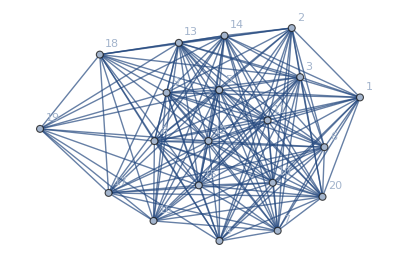

-Graphics-

```mathematica
g1=WeightedAdjacencyGraph[infBootAdjs[[1]],VertexLabels->Automatic]

CommunityGraphPlot[g1,Drop[comms[[1]],-1]]
```

```mathematica
FromLetterNumber[Drop[comms[[1]],-1]]
```

{{a,b,c,d,e,f,g,h,i,j,k,t},{l,m,n,o,p,q,r,s}}

```mathematica
comms[[1]]
```

{{1,2,3,4,5,6,7,8,9,10,11,20},{12,13,14,15,16,17,18,19},{}}

### 1.1.2b.0 Community detection via edge-betweenness/dendrogram

```mathematica
Timing[

(* this block is just naming the vertices *)
vertices={Property["a",VertexLabels->OverVector["v"]],
Property["b",VertexLabels->OverHat["j"]],
Property["c",VertexLabels->OverHat["S_z"]],
Property["d",VertexLabels->"f(x)"],
Property["e",VertexLabels->"|ψ⟩"],
Property["f",VertexLabels->"|E_2⟩"],
Property["g",VertexLabels->"⟨E_1|"],
Property["h",VertexLabels->"ψ(x)"],
Property["i",VertexLabels->"ψ^*(x)"],
Property["j",VertexLabels->"φ_3(x)"],
Property["k",VertexLabels->"φ_4^*(x)"],
Property["l",VertexLabels->OverVector["u"]·OverVector["v"]],
Property["m",VertexLabels->"⟨ψ|ψ⟩"],
Property["n",VertexLabels->"⟨E_3|ψ⟩"],
Property["o",VertexLabels->"∫ψ^*ψdx"],
Property["p",VertexLabels->"∫φ_1^*ψdx"],
Property["q",VertexLabels->"|⟨E_4|ψ⟩|^2"],
Property["r",VertexLabels->"|∫ψ^*ψdx|^2"],
Property["s",VertexLabels->"|∫φ_2^*ψdx|^2"],
Property["t",VertexLabels->"⟨ψ|"]};

vertexLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};

nVerts=Length@vertices;


(* initializing the list where we will store the lists of edgeweights from each bootstrapped adjacency matrix *)
varEdgeWeights=Table[{},nBoots];


(* Here we fill in the lists of edgeweights for each bootstrapped adjacency matrix. Worth pointing out that "j<k" is actually important, as it allows the order of the weights in each varEdgeWeights sublist to match the order of the edges themselves when using EdgeList[] on the WeightedAdjacencyGraph[]s we will find immediately after this step *)
For[i=1,i<=nBoots,i++,
For[j=1,j<=nExp,j++,
For[k=1,k<=nExp,k++,
If[j<k&&bootAdjs[[i,j,k]]!=0,
varEdgeWeights[[i]]=Append[varEdgeWeights[[i]],bootAdjs[[i,j,k]]]
]
]
]
];


(* here we define a new version of the bootstrapped adjacency matrices, where we will swap out the zeroes with infinities (see the note below) *)
infBootAdjs=bootAdjs;

(* WeightedAdjacencyGraph[] takes an edge weight of Infinity to mean no edge (I guess to distinguish between no edge at all and edges of weight zero?)  We don't care about that distinction, so we set all zeroes within our weighted adjacency matrix to infinity when we want to generate weighted graphs from them *)
For[i=1,i<=nBoots,i++,
For[j=1,j<=Length@vertices,j++,
For[k=1,k<=Length@vertices,k++,
If[infBootAdjs[[i,j,k]]==0,
infBootAdjs[[i,j,k]]=Infinity
]
]
]
];


(* Here we gather the lists of edges in each graph in a list called wEdgeLists (in the same order as their associated weights are in varEdgeWeights *)
wEdgeLists=Table[0,nBoots];
For[i=1,i<=nBoots,i++,
wEdgeLists[[i]]=EdgeList[WeightedAdjacencyGraph[vertices,infBootAdjs[[i]]]]
];


(* generate weighted graphs for each bootstrapped network and stores them in "wGraphs" *)
wGraphs=Table[0,nBoots];
For[i=1,i<=nBoots,i++,
wGraphs[[i]]=WeightedAdjacencyGraph[vertices,infBootAdjs[[i]]]
];


(* here I am defining "maxEdges" as the number of edges in the graph with the most edges. This will be used to help make the lists of the graphs work--there will just be zeroes at the ends of the rows with fewer edges *)
nEdges=Table[0,nBoots];
For[i=1,i<=nBoots,i++,
nEdges[[i]]=Length@wEdgeLists[[i]]
];
maxEdges=Max[nEdges];


(* calculates the centrality weights for all of the edges in each of the bootstrapped networks. The normalization-looking thing there is to have each N-weighted edge to effectively count as N different single-weight edges for the calculation *)
wCents=Table[0,nBoots];
For[i=1,i<=nBoots,i++,
wCents[[i]]=EdgeBetweennessCentrality[wGraphs[[i]]]/varEdgeWeights[[i]]
];


(* here I initialize the lists that will keep track of the edges that are removed in each step of the algorithm for each bootstrapped network (in the order in which they are removed) *)
removeLists=Table[{},nBoots];


(* initializes the table where we'll store the timelapse frames for each step in the algorithm for each bootstrapped networks *)
tlGs=Table[0,nBoots,maxEdges];


(* here we initialize "hiCentrLists", a table that will store which edge had the highest centrality scores for each step in the algorithm *)
hiCentrLists=Table[0,nBoots,maxEdges];


(* here we initialize the variable where we will store the position of the edge with highest centrality in the network at each step *)
hiCentrPos=Table[0,nBoots];


(* here we initialize tables where we will store the number of communities for each network (which will be updated throughout the algorithm), as well as the communities themselves, specifically updating whenever a new community splits off *)
nComms=Table[0,nBoots,maxEdges];
commsList=Table[0,nBoots,nVerts];


(* here we actually run the edge-betweenness algorithm for each bootstrapped network *)
For[i=1,i<=nBoots,i++,
For[j=1,j<=nEdges[[i]],j++,

(* redefines hiCentrPos each step through the algorithm as the position of the largest number in the ith sublist of wCents (i.e., records which edge has the highest centrality just before removing the jth edge, for the ith initial network) *)
hiCentrPos=Ordering[wCents[[i]],-1][[1]];

(* records which edge from the ith initial graph is the jth one to be removed (has the highest centrality at the jth step in the algorithm) *)
hiCentrLists[[i,j]]=EdgeList[wGraphs[[i]]][[hiCentrPos]];

(* slots in the timelapse graphs for each step of the algorithm for each different initial network--these will be used to calculate the betweennesses *)
tlGs[[i,j]]=Graph[vertices,wEdgeLists[[i]],EdgeWeight->varEdgeWeights[[i]],ImageSize->Large];

(* removes the edge with the largest betweenness centrality, as well as its associated weight and centrality score *)
wCents[[i]]=Delete[wCents[[i]],hiCentrPos];
wEdgeLists[[i]]=Delete[wEdgeLists[[i]],hiCentrPos];
varEdgeWeights[[i]]=Delete[varEdgeWeights[[i]],hiCentrPos];

(* redefines the graph now that we've removed the offending edge, for use in recalculating the new highest-betweenness edge *)
tlGs[[i,j]]=Graph[vertices,wEdgeLists[[i]],EdgeWeight->varEdgeWeights[[i]]];

(* writes down how many communities we have, now that we've removed the latest edge *)
nComms[[i,j]]=Length@ConnectedComponents[tlGs[[i,j]]];

(* if we've created a new community (meaning an existing one has split), addes the current component breakdown to the commsList *)
If[nComms[[i,j]]>nComms[[i,j-1]],
commsList[[i,nComms[[i,j-1]]]]=ConnectedComponents[tlGs[[i,j]]]
];

(* if we've reached the point were everything is disconnected (the number of communities is equal to the number of vertices), we break out of the loop.  This probably isn't necessary, but we could potentially change this value to stop the process at any number of communities we may want *)
If[Length@ConnectedComponents[tlGs[[i,j]]]==nVerts,
Break[]
];

(* recalculates the weighted betweennesses, now that we've made a new network *)
wCents[[i]]=EdgeBetweennessCentrality[tlGs[[i,j]]]/varEdgeWeights[[i]]

]
];


(* for convenience (and so I don't overwrite the commsList), we define a new variable to work with, where we will take only the first letter of each community's vertex labels, as that should make comparisons easier *)
firstLetterCommsList=commsList;

(* here we do what is described above--turning each list of vertices within a community into a single non-list one-letter string for the alphabeticallyt first vertex in each community *)
For[i=1,i<=nBoots,i++,
For[j=1,j<=nVerts-1,j++,
Do[firstLetterCommsList[[i,j,n]]=First[firstLetterCommsList[[i,j,n]]],
{n,j+1}
];
(* and we'll alphabetize them as well, cuz while it *shouldn't* be an issue of them getting mixed around, might as well make sure, eh? *)
firstLetterCommsList[[i,j]]=Sort[firstLetterCommsList[[i,j]]]
]
];


(* here we collect some interesting data: we collect in the first two lists within lastNumComm the two dendrograms that differ, and in the third list the number of communities that the two associated dendrograms had agreement on (i.e., in the step before they eventually disagreed) *)
 lastNumComm=Table[{},3];

For[i=1,i<=nBoots,i++,
For[j=1,j<=nBoots,j++,
If[i<j,
For[k=1,k<=nVerts-1,k++,
If[firstLetterCommsList[[i,k]]!=firstLetterCommsList[[j,k]],
lastNumComm[[1]]=Append[lastNumComm[[1]],i];
lastNumComm[[2]]=Append[lastNumComm[[2]],j];
lastNumComm[[3]]=Append[lastNumComm[[3]],k-1];
(*
Print[i," ",j," ",k];
*)
Break[]
]
]
]
]
];

]

(* here we export the main outputs from this chunk, as this takes wayyyyyy too long to compute. Turns out exporting them as .wxf allows for pretty much anything to be exported, as long as we intend to import it back into Mathematica to work with it more *)
SetDirectory[NotebookDirectory[]];
Export["F21+F22SpinsBootstrappingLastNumComm.wxf",lastNumComm];
Export["F21+F22SpinsBootstrappingFirstLetterCommsList.wxf",firstLetterCommsList];
Export["F21+F22SpinsBootstrappingCommsList.wxf",commsList];
Export["F21+F22SpinsBootstrappingTLGs.wxf",tlGs];
```

{2703.66,Null}

### 1.1.2b.1 Import files from edge-betweenness

```mathematica
SetDirectory[NotebookDirectory[]];

(* here we import the files we saved after doing the 45 mins of edge-betweenness, to spare us from having to run that again. Note that they are .wxf files, as this is a generic format for use within/between Mathematica documents that can handle any kind of data (graphs, multidimensional arrays, etc.) *)
lastNumComm=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsBootstrappingLastNumComm.wxf"];
firstLetterCommsList=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsBootstrappingFirstLetterCommsList.wxf"];
commsList=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsBootstrappingCommsList.wxf"];
(*
tlGs=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21\\All Spins\\F21SpinsBootstrappingTLGs.wxf"];
*)

nVerts=20;
nBoots=1000;
```

### 1.1.2b.2 Analyzing community structure among bootstrapped networks

#### Using stacked bar charts

{728,270,2}

({728,270}
{996}
{903,93}
{976}
{1000}
{725,208}
{142,353,124,175,54,55}
{94,396,102,87,97,88}
{149,569}
{92,202,54,361}
{93,196,60,354,51}
{143,54,83,269}
{89,57,80,131,114,64}
{98,78,63,97,123,57,66,66}
{64,150,247,58,52}
{302,208,91,68}
{503,71,269,74}
{873,109}
{1000})

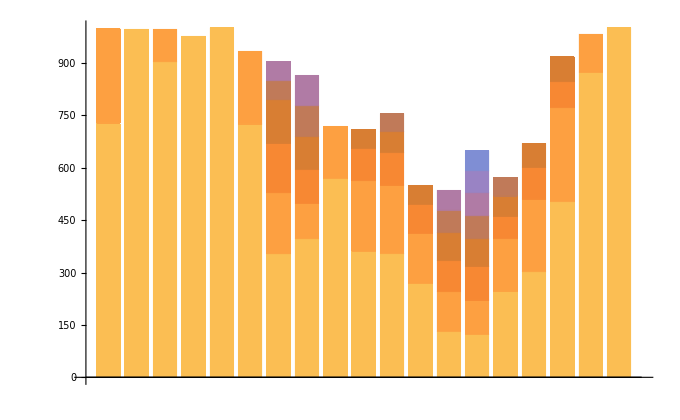

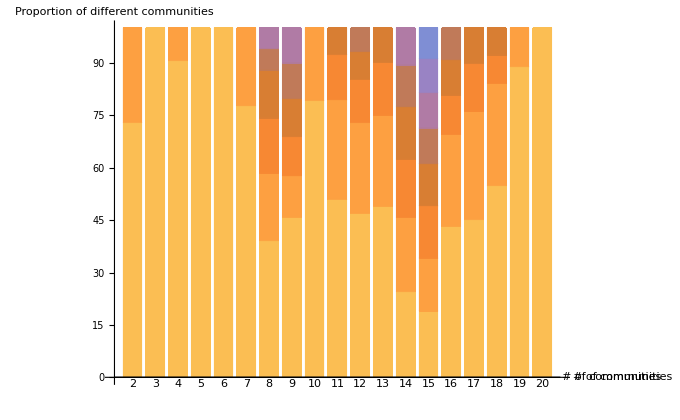

F21+F22SpinsNumPerComms.xlsx

```mathematica
(* initializing so that we can alphabetize each community in the network and then keep track of the different communities at each stage of the dendrogram *)
alphaCommsList=commsList;
diffComms=Table[0,nVerts-1];


(* here we alphabetize the elements of each community. This is necessary for successfully removing duplicate communities *)
For[k=1,k<=nBoots,k++,
For[i=1,i<=nVerts-1,i++,
For[j=1,j<=i+1,j++,
alphaCommsList[[k,i,j]]=Sort[alphaCommsList[[k,i,j]]]
]
]
]


(* here we remove duplicate community divisions, leaving only the different communities that exist at every stage of the edge-betweenness algorithm *)
For[i=1,i<=nVerts-1,i++,
diffComms[[i]]=DeleteDuplicates[alphaCommsList[[All,i]]]
]


(* here we store the number of bootstrapped networks that match a given community structure at each level of the dendrogram into the numPerComm list of lists *)
numPerComm=Table[{},nVerts-1];
For[i=1,i<=nVerts-1,i++,
For[j=1,j<=Length@diffComms[[i]],j++,
numPerComm[[i]]=Append[numPerComm[[i]],Count[alphaCommsList[[All,i]],diffComms[[i,j]]]]
]
]

(* here we remove all community layout options that account for less than 5% of the total number of dendrograms *)
cutoff=0.05*nBoots;
numPerCommCutoff=numPerComm;
For[i=1,i<=Length@numPerComm,i++,
numPerCommCutoff[[i]]=Select[numPerComm[[i]],#>=cutoff&]
]

(* this is the same as above, but for better viewing via stacked bar charts. We sort each level of the dendrogram from largest community to smallest.  This removes any information about which community structure goes with which bar *)
numPerCommCutoffSorted=numPerCommCutoff;
For[i=1,i<=Length@numPerCommCutoff,i++,
numPerCommCutoffSorted[[i]]=ReverseSort[numPerCommCutoff[[i]]]
]


numPerComm[[1]]
numPerCommCutoff//MatrixForm


BarChart[numPerCommCutoff,ChartLayout->"Stacked"];
BarChart[numPerCommCutoff,ChartLayout->"Percentile"];

BarChart[numPerCommCutoffSorted,ChartLayout->"Stacked"]
BarChart[numPerCommCutoffSorted,
ChartLayout->"Percentile",ChartLabels->{{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},None},
AxesLabel->{"# of communities","Proportion of different communities"}
]


diffComms[[6]]//MatrixForm;
numPerComm[[6]];

diffComms[[7]]//MatrixForm;
numPerComm[[7]];

diffComms[[18]]//MatrixForm;
numPerComm[[18]];

diffComms[[5]]//MatrixForm;
numPerComm[[5]];

diffComms[[6,{1,2}]]//MatrixForm;
numPerComm[[6,{1,2}]];

diffComms[[7,{1,2,4,5}]]//MatrixForm;
numPerComm[[7,{1,2,4,5}]];
Total[numPerComm[[7,{1,2,4,5}]]];

Total[numPerCommCutoff[[15]]];

Length@numPerComm[[18]];

Export["F21+F22SpinsNumPerComms.xlsx",numPerComm]
```

#### Looking at individual communities

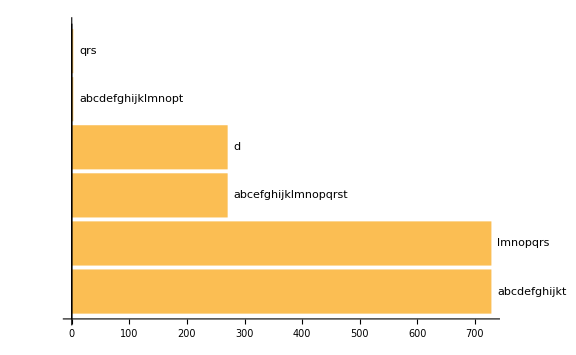
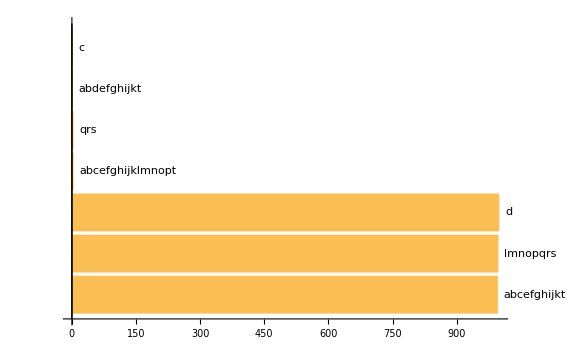
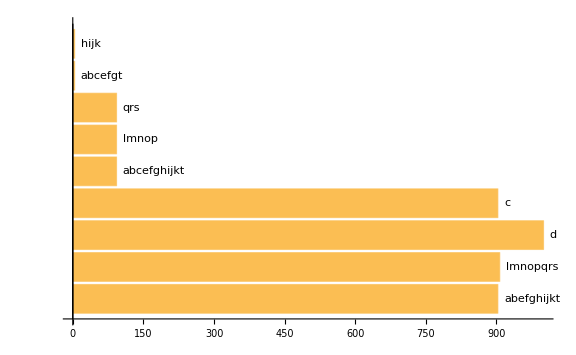
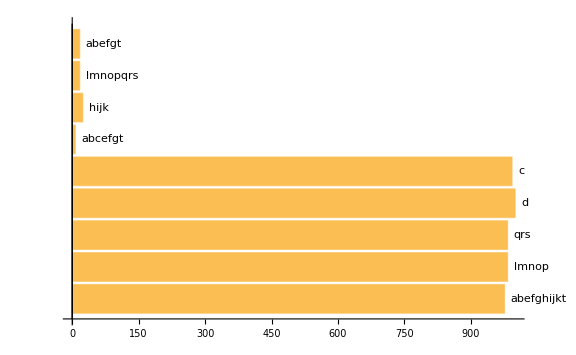
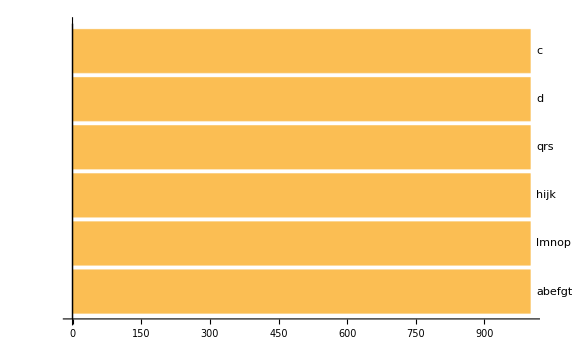
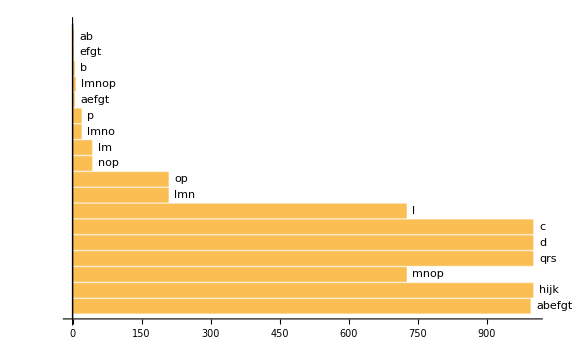
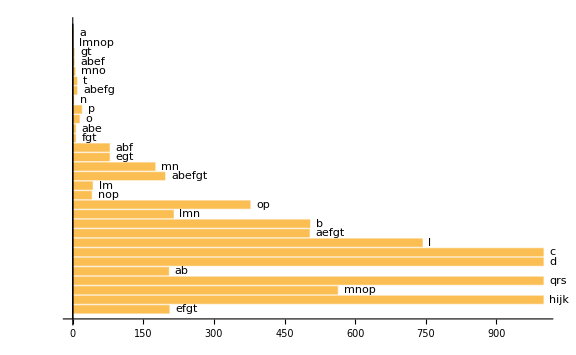
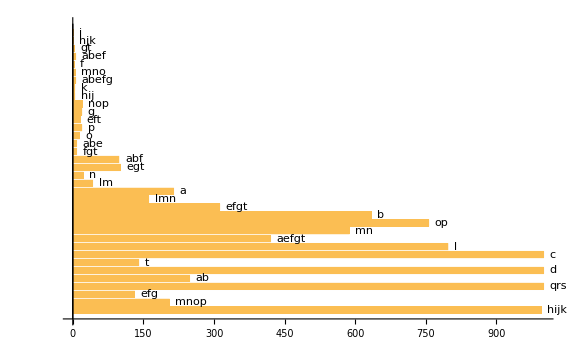
(-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-)

(728
728
270
270
2
2)

({a,b,c,d,e,f,g,h,i,j,k,t}
{l,m,n,o,p,q,r,s}
{a,b,c,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t}
{d}
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,t}
{q,r,s})

```mathematica
(* this block alphabetizes the entries in all of the commsLists, to make comparison of communities between bootstrapped instances possible *)

For[i=1,i<=nBoots,i++,
l=2;
For[j=1,j<=nVerts-1,j++,
For[k=1,k<=l,k++,
commsList[[i,j,k]]=Sort[commsList[[i,j,k]]]
];
l++
];
]


(* initializes lists to be used directly below to store communities and their proportions at each level of the dendrogram*)
propAssocs=Table[0,nVerts-1];
sepComms=Table[0,nVerts-1,2];

(* generates associations propAssocs[[i]], where the ith element is an association between all of the different communities that appear on the ith level of the dendrogram and the number of times they each appear.  sepComms is a useful way to store both the list of communities as well as the number of times they appear *)
For[i=1,i<=nVerts-1,i++,
propAssocs[[i]]=Counts[Flatten[commsList[[All,i]],1]];
sepComms[[i,1]]=Keys[propAssocs[[i]]];
sepComms[[i,2]]=Values[propAssocs[[i]]];
sepComms[[i]]=Transpose[sepComms[[i]]]
]


(* commented this out just because it takesa while (~30s) to generate the charts *)


(* initializing the lists of the labels for the bar charts and the charts themselves *)
barLabels=Table[{},nVerts-1];
bCharts=Table[0,nVerts-1];

(* here we make labels for the bar charts by concatenating all of the node letters within a given community together, as well as generate the list of bar charts at each level of the dendrogram showing the number of times each community showed up at each level among the bootstrapped networks *)
For[i=1,i<=nVerts-1,i++,
For[j=1,j<=Length@sepComms[[i]],j++,
AppendTo[barLabels[[i]],StringJoin[Transpose[sepComms[[i]]][[1,j]]]];
bCharts[[i]]=BarChart[sepComms[[i,All,2]],ChartLabels->Placed[barLabels[[i]],After],BarOrigin->Left,ImageSize->Large]
]
]



BarChart[sepComms[[1,All,2]],ChartLabels->Placed[barLabels[[1]],After],BarOrigin->Left,ImageSize->Medium];

bCharts//MatrixForm

sepComms[[1,All,2]]//MatrixForm
sepComms[[1,All,1]]//MatrixForm


sepComms[[1]]//MatrixForm;
sepComms[[2]]//MatrixForm;
sepComms[[3]]//MatrixForm;
sepComms[[4]]//MatrixForm;
sepComms[[5]]//MatrixForm;
sepComms[[6]]//MatrixForm;
sepComms[[7]]//MatrixForm;
sepComms[[8]]//MatrixForm;
```

#### Making network visualization

```mathematica
diffComms[[6]]//MatrixForm;
diffComms[[5,1]];
LetterNumber[diffComms[[5,1]]];

numPerComm[[6]]
LetterNumber[diffComms[[6,1]]]
LetterNumber[diffComms[[6,2]]]

stuAdjs=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsIndividualStudentAdjacencies.xlsx"];
wAdj=Total[stuAdjs];
wAdjInf=Round[wAdj];

For[i=1,i<=20,i++,
For[j=1,j<=20,j++,
If[wAdjInf[[i,j]]==0,
wAdjInf[[i,j]]=Infinity
]
]
]
```

{725,208,42,19,4,2}

{{1,2,5,6,7,20},{8,9,10,11},{13,14,15,16},{17,18,19},{4},{3},{12}}

{{1,2,5,6,7,20},{8,9,10,11},{12,13,14},{17,18,19},{15,16},{4},{3}}

```mathematica
(* this block is just naming the vertices *)
vertices={Property["a",VertexLabels->OverVector["v"]],
Property["b",VertexLabels->OverHat["j"]],
Property["c",VertexLabels->OverHat["S_z"]],
Property["d",VertexLabels->"f(x)"],
Property["e",VertexLabels->"|ψ⟩"],
Property["f",VertexLabels->"|E_2⟩"],
Property["g",VertexLabels->"⟨E_1|"],
Property["h",VertexLabels->"ψ(x)"],
Property["i",VertexLabels->"ψ^*(x)"],
Property["j",VertexLabels->"φ_3(x)"],
Property["k",VertexLabels->"φ_4^*(x)"],
Property["l",VertexLabels->OverVector["u"]·OverVector["v"]],
Property["m",VertexLabels->"⟨ψ|ψ⟩"],
Property["n",VertexLabels->"⟨E_3|ψ⟩"],
Property["o",VertexLabels->"∫ψ^*ψdx"],
Property["p",VertexLabels->"∫φ_1^*ψdx"],
Property["q",VertexLabels->"|⟨E_4|ψ⟩|^2"],
Property["r",VertexLabels->"|∫ψ^*ψdx|^2"],
Property["s",VertexLabels->"|∫φ_2^*ψdx|^2"],
Property["t",VertexLabels->"⟨ψ|"]};

verticesNum={Property[1,VertexLabels->OverVector["v"]],
Property[2,VertexLabels->OverHat["j"]],
Property[3,VertexLabels->OverHat["S_z"]],
Property[4,VertexLabels->"f(x)"],
Property[5,VertexLabels->"|ψ⟩"],
Property[6,VertexLabels->"|E_2⟩"],
Property[7,VertexLabels->"⟨E_1|"],
Property[8,VertexLabels->"ψ(x)"],
Property[9,VertexLabels->"ψ^*(x)"],
Property[10,VertexLabels->"φ_3(x)"],
Property[11,VertexLabels->"φ_4^*(x)"],
Property[12,VertexLabels->OverVector["u"]·OverVector["v"]],
Property[13,VertexLabels->"⟨ψ|ψ⟩"],
Property[14,VertexLabels->"⟨E_3|ψ⟩"],
Property[15,VertexLabels->"∫ψ^*ψdx"],
Property[16,VertexLabels->"∫φ_1^*ψdx"],
Property[17,VertexLabels->"|⟨E_4|ψ⟩|^2"],
Property[18,VertexLabels->"|∫ψ^*ψdx|^2"],
Property[19,VertexLabels->"|∫φ_2^*ψdx|^2"],
Property[20,VertexLabels->"⟨ψ|"]};


vertexLabels={
1->OverVector["v"],
2->OverHat["j"],
3->OverHat["S_z"],
4->"f(x)",
5->"|ψ⟩",
6->"|E_2⟩",
7->"⟨E_1|",
8->"ψ(x)",
9->"ψ^*(x)",
10->"φ_3(x)",
11->"φ_4^*(x)",
12->OverVector["u"]·OverVector["v"],
13->"⟨ψ|ψ⟩",
14->"⟨E_3|ψ⟩",
15->"∫ψ^*ψdx",
16->"∫φ_1^*ψdx",
17->"|⟨E_4|ψ⟩|^2",
18->"|∫ψ^*ψdx|^2",
19->"|∫φ_2^*ψdx|^2",
20->"⟨ψ|"
};

wAdjInf//MatrixForm;
wG=WeightedAdjacencyGraph[verticesNum,wAdjInf];

CommunityGraphPlot[wG,LetterNumber[diffComms[[6,1]]],VertexLabels->vertexLabels,PlotTheme->"Scientific",VertexLabelStyle->15]
CommunityGraphPlot[wG,LetterNumber[diffComms[[6,2]]],VertexLabels->vertexLabels,PlotTheme->"Scientific",VertexLabelStyle->15]

CommunityGraphPlot[wG,LetterNumber[diffComms[[5,1]]],VertexLabels->vertexLabels,PlotTheme->"Scientific",VertexLabelStyle->15]
```

-Graphics-

-Graphics-

-Graphics-

(0. | 0. | 0. | 0. | 1. | 1. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1.
1. | 1. | 0. | 0. | 1. | 0. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 1. | 0. | 1. | 1. | 1. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 1. | 1. | 1. | 0. | 1. | 1. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 1. | 1. | 1. | 0. | 1. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1.
1. | 1. | 0. | 0. | 1. | 1. | 1. | 1. | 1. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 1. | 1. | 0. | 0. | 0. | 0.
1. | 1. | 0. | 0. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 1. | 1. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 1. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
(* this stuff here is not being used right now, either because we don't need to reduce each community down to just their leading member, or because the bootstrapping process does not leave many dendrograms being identical (like, 0.001% of all pairs are exactly identical) *)
(*
firstLetterDiffComms=Table[0,nVerts-1];
For[i=1,i<=nVerts-1,i++,
firstLetterDiffComms[[i]]=DeleteDuplicates[firstLetterCommsList[[All,i]]]
]
*)


(*
diffArray=Table[0,nVerts-1];

(*
firstCommsList[[i,j,k]];
	i = index for the dendrogram in question (ranges from 1 - nDend);
	j = index for the step on the dendrogram (technically, the number of divisions that have happened);
	k = index for the community within that step on the dendrogram (gives the first letter alphabetically)
*)

edgeCounter=0;

For[i=1,i<=nBoots,i++,
For[j=1,j<=nBoots,j++,
If[i<j,
For[k=1,k<=nVerts-1,k++,
oncePerLayer=0;
For[l=1,l<=k+1,l++,
If[firstLetterCommsList[[i,k,l]]!=firstLetterCommsList[[j,k,l]]&&oncePerLayer==0,
diffArray[[k]]++;
oncePerLayer++
]
]
]
]
]
]
*)
```

```mathematica
commsList[[9]]//MatrixForm
```

(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
Export["numPerCommCutoff.xlsx",numPerCommCutoff]
Export["numPerCommCutoffSorted.xlsx",numPerCommCutoffSorted]
Export["numPerComm.xlsx",numPerComm]
```

numPerCommCutoff.xlsx

numPerCommCutoffSorted.xlsx

numPerComm.xlsx

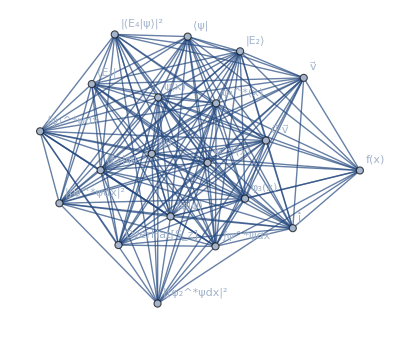

```mathematica
tlGraphs=Table[0,Length@tlGs[[1]]];
wListSpins=Table[0,Length@tlGs[[1]]];

tlGs[[1,1]]


For[i=1,i<=Length@tlGs[[1]],i++,

wListSpins[[i]]=Map[{#,PropertyValue[{tlGs[[1,i]],#},EdgeWeight]}&,EdgeList[tlGs[[1,i]]]];

tlGraphs[[i]]=SetProperty[tlGs[[1,i]],{
VertexStyle->Thread[VertexList[tlGs[[1,i]]]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[VertexDegree[[tlGs[[1,i]]]]])],
EdgeStyle->Thread[EdgeList[tlGs[[1,1]]]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[wListSpins[[i]]])]
}];
]

tlGraphs[[1]]
```

```mathematica
Dimensions[lastNumComm]
Dimensions[commsList]
Dimensions[Drop[lastNumComm,{2}]]
```

{3,499071}

{1000,20}

{2,499071}

```mathematica
(*Defining the "circle" function.  This is just for making all of the networks share the same morphology for ease of at-a-glance comparison*)
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]


tlGsNums=tlGs;
(*
For[i=1,i<=1000,i++,
For[j=1,j<=EdgeCount[tlGs[[i,1]]],j++,
tlGsNums[[i,j]]=Show[
tlGs[[i,j]],
Graphics[Text[Style[ToString[j],FontSize->30,Bold]]]
]
]
]
*)
(*
For[i=1,i<=1000,i++,
For[j=1,j<=EdgeCount[tlGs[[i,1]]],j++,
tlGsNums[[i]]=Append[
tlGsNums[[i]],
SetProperty[tlGs[[i,j]],{
VertexCoordinates->circle[20]
}
]
]
]
]
```

```mathematica
EdgeCount[tlGs[[1,2]]]
```

171

```mathematica
tlGs[[1]];
```

### Dendrogram

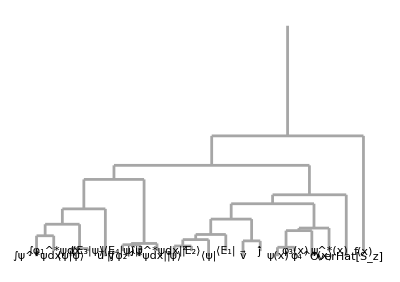

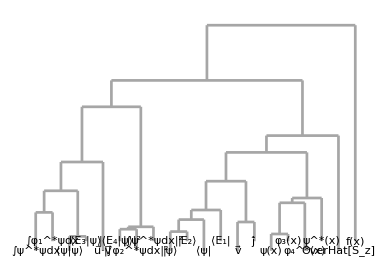

```mathematica
splitSteps={0,86,109,120,132,139,143,151,155,158,160,163,164,167,168,170,171,172,173,174};

splitHeights=174-splitSteps;

vertHeights={-6,-2,-6,-2,-6,-2,-2,-6,-2,-2,-6,-6,-6,-2,-6,-2,-2,-2,-6,-6};

heights=Join[splitHeights,vertHeights];
heightsNoStem=Drop[heights,1];

treeVerts={"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20",OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};

treeVertsNoStem={"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19",OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};

Length@heights;
Length@treeVerts;

treeEdges={
treeVerts[[1]]<->treeVerts[[2]],treeVerts[[2]]<->treeVerts[[3]],treeVerts[[2]]<->treeVerts[[24]],treeVerts[[3]]<->treeVerts[[4]],treeVerts[[3]]<->treeVerts[[5]],treeVerts[[4]]<->treeVerts[[7]],treeVerts[[4]]<->treeVerts[[16]],treeVerts[[5]]<->treeVerts[[6]],treeVerts[[5]]<->treeVerts[[23]],treeVerts[[6]]<->treeVerts[[8]],treeVerts[[6]]<->treeVerts[[10]],treeVerts[[7]]<->treeVerts[[9]],treeVerts[[7]]<->treeVerts[[32]],treeVerts[[8]]<->treeVerts[[12]],treeVerts[[8]]<->treeVerts[[15]],treeVerts[[9]]<->treeVerts[[13]],treeVerts[[9]]<->treeVerts[[20]],treeVerts[[10]]<->treeVerts[[11]],treeVerts[[10]]<->treeVerts[[29]],treeVerts[[11]]<->treeVerts[[19]],treeVerts[[11]]<->treeVerts[[31]],treeVerts[[12]]<->treeVerts[[14]],treeVerts[[12]]<->treeVerts[[27]],treeVerts[[13]]<->treeVerts[[35]],treeVerts[[13]]<->treeVerts[[36]],treeVerts[[14]]<->treeVerts[[18]],treeVerts[[14]]<->treeVerts[[40]],treeVerts[[15]]<->treeVerts[[21]],treeVerts[[15]]<->treeVerts[[22]],treeVerts[[16]]<->treeVerts[[17]],treeVerts[[16]]<->treeVerts[[38]],treeVerts[[17]]<->treeVerts[[37]],treeVerts[[17]]<->treeVerts[[39]],treeVerts[[18]]<->treeVerts[[25]],treeVerts[[18]]<->treeVerts[[26]],treeVerts[[19]]<->treeVerts[[28]],treeVerts[[19]]<->treeVerts[[30]],treeVerts[[20]]<->treeVerts[[33]],treeVerts[[20]]<->treeVerts[[34]]
};

treeEdgesNoStem={
treeVertsNoStem[[1]]<->treeVertsNoStem[[2]],treeVertsNoStem[[1]]<->treeVertsNoStem[[23]],treeVertsNoStem[[2]]<->treeVertsNoStem[[3]],treeVertsNoStem[[2]]<->treeVertsNoStem[[4]],treeVertsNoStem[[3]]<->treeVertsNoStem[[6]],treeVertsNoStem[[3]]<->treeVertsNoStem[[15]],treeVertsNoStem[[4]]<->treeVertsNoStem[[5]],treeVertsNoStem[[4]]<->treeVertsNoStem[[22]],treeVertsNoStem[[5]]<->treeVertsNoStem[[7]],treeVertsNoStem[[5]]<->treeVertsNoStem[[9]],treeVertsNoStem[[6]]<->treeVertsNoStem[[8]],treeVertsNoStem[[6]]<->treeVertsNoStem[[31]],treeVertsNoStem[[7]]<->treeVertsNoStem[[11]],treeVertsNoStem[[7]]<->treeVertsNoStem[[14]],treeVertsNoStem[[8]]<->treeVertsNoStem[[12]],treeVertsNoStem[[8]]<->treeVertsNoStem[[19]],treeVertsNoStem[[9]]<->treeVertsNoStem[[10]],treeVertsNoStem[[9]]<->treeVertsNoStem[[28]],treeVertsNoStem[[10]]<->treeVertsNoStem[[18]],treeVertsNoStem[[10]]<->treeVertsNoStem[[30]],treeVertsNoStem[[11]]<->treeVertsNoStem[[13]],treeVertsNoStem[[11]]<->treeVertsNoStem[[26]],treeVertsNoStem[[12]]<->treeVertsNoStem[[34]],treeVertsNoStem[[12]]<->treeVertsNoStem[[35]],treeVertsNoStem[[13]]<->treeVertsNoStem[[17]],treeVertsNoStem[[13]]<->treeVertsNoStem[[39]],treeVertsNoStem[[14]]<->treeVertsNoStem[[20]],treeVertsNoStem[[14]]<->treeVertsNoStem[[21]],treeVertsNoStem[[15]]<->treeVertsNoStem[[16]],treeVertsNoStem[[15]]<->treeVertsNoStem[[37]],treeVertsNoStem[[16]]<->treeVertsNoStem[[36]],treeVertsNoStem[[16]]<->treeVertsNoStem[[38]],treeVertsNoStem[[17]]<->treeVertsNoStem[[24]],treeVertsNoStem[[17]]<->treeVertsNoStem[[25]],treeVertsNoStem[[18]]<->treeVertsNoStem[[27]],treeVertsNoStem[[18]]<->treeVertsNoStem[[29]],treeVertsNoStem[[19]]<->treeVertsNoStem[[32]],treeVertsNoStem[[19]]<->treeVertsNoStem[[33]]
};

spinTree=TreeGraph[treeVerts,treeEdges,VertexLabels->"Name",VertexWeight->heights];
spinTreeNoStem=TreeGraph[treeVertsNoStem,treeEdgesNoStem,VertexLabels->"Name",VertexWeight->heightsNoStem];



Dendrogram[spinTree]/.Line[x_]:>{Thickness[0.005],Line[x]}
Dendrogram[spinTreeNoStem]/.Line[x_]:>{Thickness[0.005],Line[x]}
```